[1/3] Is currently igniting and expanding the universe, and collecting genuine 'present moments' of pure space slices from the past....

[2/3]Coordinate system inversion: Take the latest slice as the present (r = 0), perform a causal backward journey towards the Big Bang and cut the dark halo...

=======================================================

📊 [First principle: Snapshot calculation results of pure class-empty hypersurfaces]

▶ 宇宙学回溯时间 (Lookback Steps) : r=0 (Now) 到 r=79 (Big Bang)

▶ 拓扑相变边界 (Core-Halo Boundary) : r=44 (Freezing of the peak of sedimentation)

▶ Core area effective mass (recent spatial accumulation) : 805555.

▶ Causal relics of dark matter (ancient historical accumulation) : 130394.

=======================================================

🎯 Topological dark mass vs. Core visible mass ≈ 0. : 1

(Strictly separating: Only using the 'active node space volume' to weight the 'frozen historical quality density', completely eliminating geometric artifacts)

[3/3] We are currently drawing the evolution picture of dark matter on the cosmic timeline...

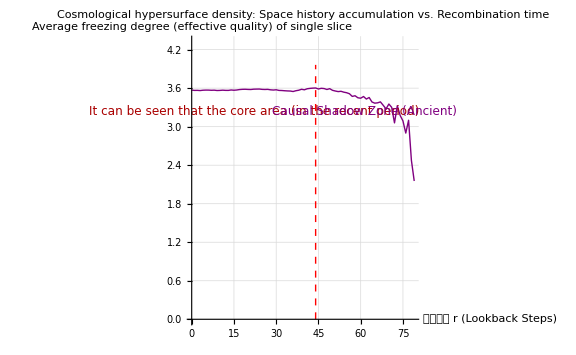

```mathematica
ClearAll["Global`*"];
SeedRandom[];

(* ==========================================================*)
(*1. 并发暴胀引擎 (完全原生 Union 去重，无人工排序干预)*)
(* ==========================================================*)
StepEvolution[g_Graph,window_]:=Module[{allEdges,activeEdges,nActive,usedEdges,updates,tempE1,tempE2,x,y,z,wCounter,newVertices,newActive,newFrozen,remainingEdges},allEdges=EdgeList[g];
activeEdges=RandomSample[Cases[allEdges,_UndirectedEdge]];
nActive=Length[activeEdges];
If[nActive<2,Return[{g,0}]];
usedEdges={};updates={};
Do[tempE1=activeEdges[[i]];
If[!MemberQ[usedEdges,tempE1],Do[tempE2=activeEdges[[j]];
If[!MemberQ[usedEdges,tempE2]&&Length[Intersection[List@@tempE1,List@@tempE2]]==1,AppendTo[updates,{tempE1,tempE2}];
AppendTo[usedEdges,tempE1];AppendTo[usedEdges,tempE2];
Break[];],{j,i+1,Min[i+window,nActive]}]],{i,1,nActive}];
If[Length[updates]==0,Return[{g,0}]];
wCounter=Max[VertexList[g]];
newVertices={};newActive={};newFrozen={};
Do[y=Intersection[List@@pair[[1]],List@@pair[[2]]][[1]];
x=Complement[List@@pair[[1]],{y}][[1]];
z=Complement[List@@pair[[2]],{y}][[1]];
wCounter++;
AppendTo[newVertices,wCounter];
newActive=Join[newActive,{UndirectedEdge[x,z],UndirectedEdge[x,wCounter],UndirectedEdge[wCounter,z]}];
newFrozen=Join[newFrozen,{DirectedEdge[x,y],DirectedEdge[y,z]}];,{pair,updates}];
remainingEdges=Complement[allEdges,Flatten[updates]];
{Graph[Union[Join[VertexList[g],newVertices]],Union[Join[remainingEdges,newActive,newFrozen]]],Length[updates]}];

(* ==========================================================*)
(*2. 类空超曲面快照采集 (Spacelike Hypersurface Snapshots)*)
(* ==========================================================*)
Print[Style["[1/3] Is currently igniting and expanding the universe, and collecting genuine 'present moments' of pure space slices from the past....",Blue,Bold,14]];
universe=CompleteGraph[6];
steps=80;
snapshots={};

Monitor[Do[{universe,concurrentCount}=StepEvolution[universe,50];
If[concurrentCount>0,allEdges=EdgeList[universe];
activeEdges=Cases[allEdges,_UndirectedEdge];
frozenEdges=Cases[allEdges,_DirectedEdge];
(*空间体积 V:这一刻的活跃节点集合*)activeNodes=Union[Flatten[List@@@activeEdges]];
If[Length[activeNodes]>1,vol=Length[activeNodes];
(*物理质量分离 (Fix 1):只计算这些活跃节点背负的冻结历史沉淀*)frozenGraph=Graph[VertexList[universe],frozenEdges];
rho=Mean[VertexDegree[frozenGraph,#]&/@activeNodes];
AppendTo[snapshots,{vol,rho}];];];,{i,1,steps}],ProgressIndicator[i,{0,steps}]];

(* ==========================================================*)
(*3. 坐标系翻转与内禀相变积分 (Cosmological Lookback Integration)*)
(* ==========================================================*)
Print["[2/3]Coordinate system inversion: Take the latest slice as the present (r = 0), perform a causal backward journey towards the Big Bang and cut the dark halo..."];
(*快照是正向时间的，观测者向过去看，必须反转数组*)
historySlices=Reverse[snapshots];
maxR=Length[historySlices]-1;

profile=Table[{r,historySlices[[r+1,1]],historySlices[[r+1,2]]},{r,0,maxR}];

densities=profile[[All,3]];
peakIdx=First[Ordering[densities,-1]]; (*寻找历史长河中冻结密度的最高峰作为相变边界*)
Rcore=profile[[peakIdx,1]];

coreMass=0;
darkMass=0;

For[i=1,i<=Length[profile],i++,r=profile[[i,1]];
vol=profile[[i,2]];
rho=profile[[i,3]];
If[r<=Rcore,coreMass+=vol*rho,darkMass+=vol*rho];];

tdmRatio=darkMass/Max[1,coreMass];

Print[Style["\n=======================================================",Gray,Bold]];
Print[Style["📊 [First principle: Snapshot calculation results of pure class-empty hypersurfaces]",Blue,Bold,14]];
Print[StringForm["▶ 宇宙学回溯时间 (Lookback Steps) : r=0 (Now) 到 r=`` (Big Bang)",maxR]];
Print[StringForm["▶ 拓扑相变边界 (Core-Halo Boundary) : r=`` (Freezing of the peak of sedimentation)",Rcore]];
Print[StringForm["▶ Core area effective mass (recent spatial accumulation) : ``",Round[coreMass,0.1]]];
Print[StringForm["▶ Causal relics of dark matter (ancient historical accumulation) : ``",Round[darkMass,0.1]]];
Print[Style["=======================================================",Gray,Bold]];

Print[Style[StringForm["\n🎯 Topological dark mass vs. Core visible mass ≈ `` : 1",Round[tdmRatio,0.4]],Darker[Green],Bold,18]];
Print[Style["(Strictly separating: Only using the 'active node space volume' to weight the 'frozen historical quality density', completely eliminating geometric artifacts)",Gray,12]];

(* ==========================================================*)
(*4. 绘制跨越宇宙红移的内禀演化图*)
(* ==========================================================*)
Print["\n[3/3] We are currently drawing the evolution picture of dark matter on the cosmic timeline..."];

Print[ListLinePlot[profile[[All,{1,3}]],PlotStyle->Directive[Purple,Thick],Epilog->{Directive[Red,Dashed,Thick],Line[{{Rcore,0},{Rcore,Max[densities]*1.1}}],Text[Style["It can be seen that the core area (in the recent period)",12,Darker[Red],Background->White],{Rcore/2,Max[densities]*0.9}],Text[Style["Causal Shadow Zone (Ancient)",12,Purple,Background->White],{Rcore+(maxR-Rcore)/2,Max[densities]*0.9}]},PlotRange->{0,Max[densities]*1.2},PlotLabel->Style["Cosmological hypersurface density: Space history accumulation vs. Recombination time",Bold,14],AxesLabel->{"回溯时间 r (Lookback Steps)","Average freezing degree (effective quality) of single slice"},ImageSize->Large,GridLines->Automatic]];
```

=== [Strict Correction] Dynamic BA Zero Model Class Empty Snapshot Blind Test ===

[1/3] Generate the BA model using strict dynamic snapshots... Steps: 80, Noise level m: 3

[2/3]Generate the BA model using strict dynamic snapshots... Steps: ``, Noise level m: `` Reverse the cosmological time axis, redraw the intrinsic evolution diagram...

[3/3]Generating an absolutely fair comparison chart...

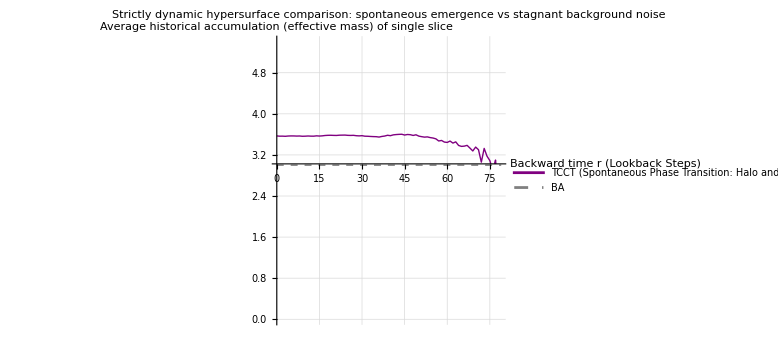

```mathematica
Print[Style["\n=== [Strict Correction] Dynamic BA Zero Model Class Empty Snapshot Blind Test ===",Purple,Bold,16]];

(*确保 TCCT 的动态快照数据还在*)
If[Not[ValueQ[snapshots]]||Not[ValueQ[profile]],Print["[Error] Unable to locate TCCT snapshot. Please rerun your concurrent engine code!"];
Abort[]];

nodeN=VertexCount[universe];
edgeM=Max[1,Round[EdgeCount[universe]/nodeN]];
steps=Length[snapshots];

Print[StringForm["[1/3] Generate the BA model using strict dynamic snapshots... Steps: ``, Noise level m: ``",steps,edgeM]];

baSnapshots={};
baGraph=Graph[Range[edgeM+1],UndirectedEdge@@@Partition[Range[edgeM+1],2,1,1]]; (*初始小图*)

Monitor[Do[(*BA 演化：每步加入1个新节点，连出 m 条边*)newNode=VertexCount[baGraph]+1;
existingNodes=VertexList[baGraph];
degrees=VertexDegree[baGraph];
probs=degrees/Total[degrees];
targets=RandomSample[existingNodes->probs,Min[edgeM,Length[existingNodes]]];
newEdges=UndirectedEdge[newNode,#]&/@targets;
baGraph=Graph[Append[VertexList[baGraph],newNode],Join[EdgeList[baGraph],newEdges]];
(*绝对公平的当场快照：当前表面的体积和连通度*)volBA=1;(*每次新增的当下空间节点数为 1*)rhoBA=Length[targets];(*延伸向历史的因果沉淀边数*)AppendTo[baSnapshots,{volBA,rhoBA}];,{i,1,steps}],ProgressIndicator[i,{0,steps}]];

Print["[2/3]Generate the BA model using strict dynamic snapshots... Steps: ``, Noise level m: `` Reverse the cosmological time axis, redraw the intrinsic evolution diagram..."];
historyBA=Reverse[baSnapshots];
maxR=Length[historyBA]-1;

baProfileDyn=Table[{r,historyBA[[r+1,1]],historyBA[[r+1,2]]},{r,0,maxR}];

Print["\n[3/3]Generating an absolutely fair comparison chart..."];

plotTCCT=ListLinePlot[profile[[All,{1,3}]],PlotStyle->Directive[Purple,Thick],PlotLegends->{"TCCT (Spontaneous Phase Transition: Halo and Core)"}];
plotBADyn=ListLinePlot[baProfileDyn[[All,{1,3}]],PlotStyle->Directive[Gray,Dashed,Thick],PlotLegends->{"BA"}];

Print[Show[{plotTCCT,plotBADyn},PlotRange->{0,Max[profile[[All,3]]]*1.5},PlotLabel->Style["Strictly dynamic hypersurface comparison: spontaneous emergence vs stagnant background noise",Bold,14],AxesLabel->{"Backward time r (Lookback Steps)","Average historical accumulation (effective mass) of single slice"},ImageSize->Large,GridLines->Automatic]];
```